```mathematica
(*Some General Values*)
```

```mathematica
α = 1;
β = 1;
γ = 0.1;
```

```mathematica
(*Some General Matrices*)
R[θ_]:={{Cos[2θ],Sin[2θ]},{Sin[2θ],-Cos[2θ]}}
```

```mathematica
P[θ_]:=(1/2)(IdentityMatrix[2]-R[θ])
Pt[θ_]:=(1/2)(IdentityMatrix[2]-R[θ+Pi/2])
```

```mathematica
Pp =P[Pi/3];
Pm = P[5Pi/3];
P0 = P[0];
Ppt =Pt[Pi/3];
Pmt = Pt[5Pi/3];
P0t = Pt[0];
jmat = {{0,-1},{1,0}};
Omat ={{0,0},{0,0}}; 
(*n is hight m is circumphrince, and n2 is hight of second cylender*)
n=1;
m=20;
n2=m;
```

```mathematica
(*Define Matrices*)
(*-------------------------------------*)
```

```mathematica
(*The Blue Matrices are associated to the periodic edges*)
```

```mathematica
pblue = ArrayFlatten[TensorProduct[ArrayFlatten[TensorProduct[IdentityMatrix[(n+1)],{{1,-1},{-1,1}}]],Pp]];
pblueT = ArrayFlatten[TensorProduct[ArrayFlatten[TensorProduct[IdentityMatrix[(n+1)],{{1,-1},{-1,1}}]],Ppt]];

pblue2 = ArrayFlatten[TensorProduct[ArrayFlatten[TensorProduct[IdentityMatrix[(n2+1)],{{1,-1},{-1,1}}]],Pp]];
pblueT2 = ArrayFlatten[TensorProduct[ArrayFlatten[TensorProduct[IdentityMatrix[(n2+1)],{{1,-1},{-1,1}}]],Ppt]];
```

```mathematica
(*The Red Matrices first need to have their center defined then we add on the edge terms*)
```

```mathematica
predcenter = ArrayFlatten[TensorProduct[ArrayFlatten[TensorProduct[IdentityMatrix[(n+1)-1],{{1,-1},{-1,1}}]],P0]];
predcenterT = ArrayFlatten[TensorProduct[ArrayFlatten[TensorProduct[IdentityMatrix[(n+1)-1],{{1,-1},{-1,1}}]],P0t]];

predcenter2 = ArrayFlatten[TensorProduct[ArrayFlatten[TensorProduct[IdentityMatrix[(n2+1)-1],{{1,-1},{-1,1}}]],P0]];
predcenterT2 = ArrayFlatten[TensorProduct[ArrayFlatten[TensorProduct[IdentityMatrix[(n2+1)-1],{{1,-1},{-1,1}}]],P0t]];
```

```mathematica
pred2=ArrayFlatten[{{P0,0,-P0},{0,predcenter,0},{-P0,0,P0}}];
pred2T=ArrayFlatten[{{P0t,0,-P0t},{0,predcenterT,0},{-P0t,0,P0t}}];
pred1=ArrayFlatten[{{Omat,0,Omat},{0,predcenter,0},{Omat,0,Omat}}];
pred1T=ArrayFlatten[{{Omat,0,Omat},{0,predcenterT,0},{Omat,0,Omat}}];

pred22=ArrayFlatten[{{P0,0,-P0},{0,predcenter2,0},{-P0,0,P0}}];
pred2T2=ArrayFlatten[{{P0t,0,-P0t},{0,predcenterT2,0},{-P0t,0,P0t}}];
pred12=ArrayFlatten[{{Omat,0,Omat},{0,predcenter2,0},{Omat,0,Omat}}];
pred1T2=ArrayFlatten[{{Omat,0,Omat},{0,predcenterT2,0},{Omat,0,Omat}}];
```

```mathematica
(*The Green Matrices are functions of w a root of unity and k to cicle between the roots*)
```

```mathematica
pgreen[w_,k_]:=ArrayFlatten[TensorProduct[ArrayFlatten[TensorProduct[IdentityMatrix[(n+1)],{{1 ,-(w^-k) },{-(w^k) ,1 }}]],Pm]];
pgreenT[w_,k_]:=ArrayFlatten[TensorProduct[ArrayFlatten[TensorProduct[IdentityMatrix[(n+1)],{{1 ,-w^k },{-(w^(-k)) ,1 }}]],Pmt]];

pgreen2[w_,k_]:=ArrayFlatten[TensorProduct[ArrayFlatten[TensorProduct[IdentityMatrix[(n2+1)],{{1 ,-(w^-k) },{-(w^k) ,1 }}]],Pm]];
pgreenT2[w_,k_]:=ArrayFlatten[TensorProduct[ArrayFlatten[TensorProduct[IdentityMatrix[(n2+1)],{{1 ,-w^k },{-(w^(-k)) ,1 }}]],Pmt]];
```

```mathematica
(*a Matrix that is just 4nx4n zero, probably a better way to define this*)
```

```mathematica
large0Mat = ConstantArray[ConstantArray[0,4n],4n];

large0Mat2 = ConstantArray[ConstantArray[0,4n2],4n2];
```

```mathematica
(*uses Large 0Mat as the center term*)
```

```mathematica
plambda = ArrayFlatten[{{β jmat.P0+γ jmat. P0t,0,-β jmat.P0-γ jmat .P0t},{0,large0Mat,0},{-β jmat.P0-γ jmat .P0t,0,β jmat.P0+γ jmat. P0t}}];

plambda2 = ArrayFlatten[{{β jmat.P0+γ jmat. P0t,0,-β jmat.P0-γ jmat .P0t},{0,large0Mat2,0},{-β jmat.P0-γ jmat .P0t,0,β jmat.P0+γ jmat. P0t}}];
```

```mathematica
(*adding all of the above matrices together, D1 is periodic and D2 is Doubly periodic*)
```

```mathematica
DPeriodic1[k_] := α(IdentityMatrix[4(n+1)])+β(pblue+pred1+pgreen[E^(2 Pi I/m),k])+γ(pblueT+pred1T+pgreenT[E^(2 Pi I/m),k]);
DPeriodic2[k_] := α(IdentityMatrix[4(n+1)])+β(pblue+pred2+pgreen[E^(2 Pi I/m),k])+γ(pblueT+pred2T+pgreenT[E^(2 Pi I/m),k]);

DPeriodic1square[k_] := α(IdentityMatrix[4(n2+1)])+β(pblue2+pred12+pgreen2[E^(2 Pi I/m),k])+γ(pblueT2+pred1T2+pgreenT2[E^(2 Pi I/m),k]);
DPeriodic1squaretorus[k_] := α(IdentityMatrix[4(n2+1)])+β(pblue2+pred22+pgreen2[E^(2 Pi I/m),k])+γ(pblueT2+pred2T2+pgreenT2[E^(2 Pi I/m),k]);
```

```mathematica
(*Define jmat, one should note the above is acturally just D and we have to multiply by Jmat*)
```

```mathematica
jmatLarge = ArrayFlatten[TensorProduct[IdentityMatrix[Length[DPeriodic2[1]]/2],{{0,-1},{1,0}}]];

jmatLarge2 = ArrayFlatten[TensorProduct[IdentityMatrix[Length[DPeriodic1square[1]]/2],{{0,-1},{1,0}}]];
```

```mathematica
(*----------------------------------------------------------*)
```

```mathematica
(*gap crossing stuff*)
length=Length[Select[Round[ Eigenvalues[I jmatLarge2.DPeriodic1square[1]],0.000000001],Positive]];
```

```mathematica
rangesigmasmall=ArrayReshape[Flatten[Table[Table[{j,Select[Round[ Eigenvalues[I jmatLarge.DPeriodic1[j]],0.000000001],Positive][[i]]},{i,1,Length[Select[Round[ Eigenvalues[I jmatLarge.DPeriodic1[1]],0.000000001],Positive]]}],{j,1,m}]],{m Length[Select[Round[ Eigenvalues[I jmatLarge.DPeriodic1[1]],0.000000001],Positive]],2}];

rangesigmabig=ArrayReshape[Flatten[Table[Table[{j,Select[Round[ Eigenvalues[I jmatLarge2.DPeriodic1square[j]],0.000000001],Positive][[i]]},{i,1,length}],{j,1,m}]],{m length,2}];
```

```mathematica
rangesigmabigtorus=ArrayReshape[Flatten[Table[Table[{j,Select[Round[ Eigenvalues[I jmatLarge2.DPeriodic1squaretorus[j]],0.000000001],Positive][[i]]},{i,1,length}],{j,1,m}]],{m length,2}];
```

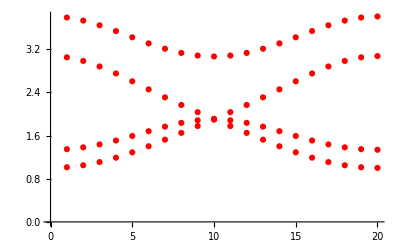

```mathematica
smallSigmaRangePlot=ListPlot[ rangesigmasmall,PlotStyle->Red]
```

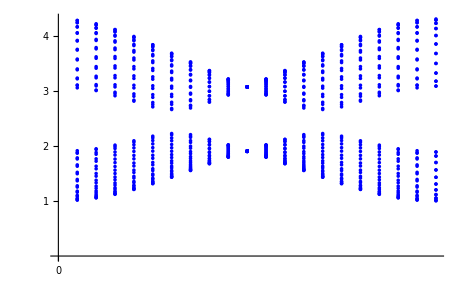

```mathematica
bigSigmaRnagePlottorus1=ListPlot[rangesigmabigtorus,PlotStyle->Blue,TicksStyle->Large,Ticks-> {{0,{25,Pi/2},{50,Pi},{75,3Pi/2},{100,2Pi}},{1,2,3,4}}]
```

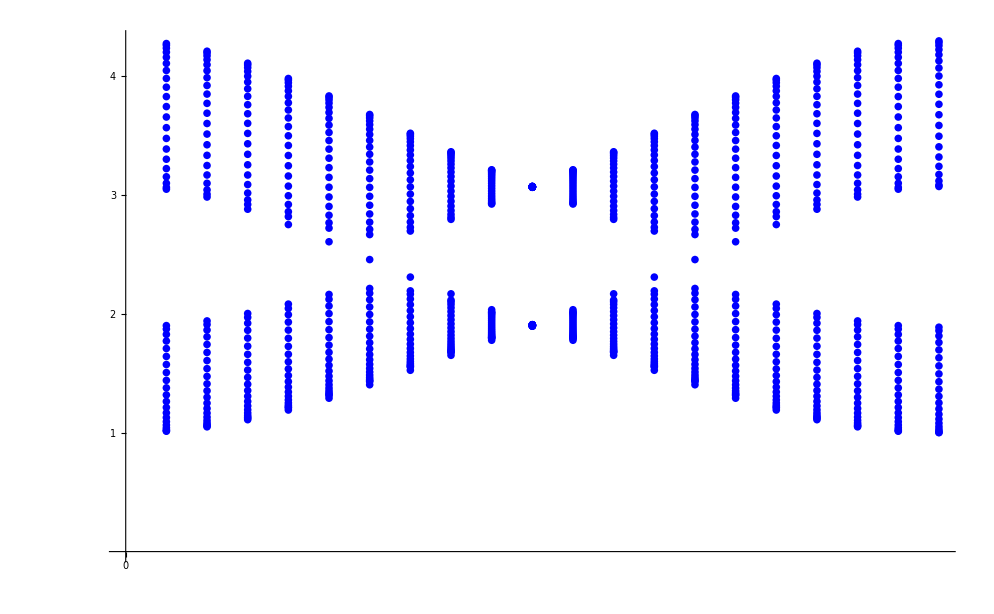

```mathematica
bigSigmaRnagePlot1=ListPlot[rangesigmabig,PlotStyle->Blue,TicksStyle->Large,Ticks-> {{0,{25,Pi/2},{50,Pi},{75,3Pi/2},{100,2Pi}},{1,2,3,4}}]
```